```mathematica
aa[f_,n_,s_]:=n(1/n Sum[(j/n)^(-1/2)f[s Log[j/n]],{j,1,n}]-Integrate[f[s Log[x]]/x^(1/2),{x,0,1}])
```

```mathematica
DiscretePlot[aa[Sin,n,10],{n,1,100}]
```

$Aborted

```mathematica
Integrate[Sin[s Log[x]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[-(4 s)/(1+4 s^2),-1/2<Im[s]<1/2]

```mathematica
Integrate[Cos[s Log[x]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[2/(1+4 s^2),s∈Reals]

```mathematica
Integrate[Tan[s Log[x]]/x^(1/2),{x,0,1}]
```

$Aborted

```mathematica
Integrate[s Log[x]/x^(1/2),{x,0,1}]
```

-4 s

```mathematica
Integrate[(s Log[x])^2/x^(1/2),{x,0,1}]
```

16 s^2

```mathematica
Integrate[Log[s Log[x]]/x^(1/2),{x,0,1}]
```

-2 EulerGamma+2 Log[-2 s]

```mathematica
Integrate[Sinh[s Log[x]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[(4 s)/(-1+4 s^2),-1/2<s<1/2]

```mathematica
Integrate[Exp[s Log[x]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[2/(1+2 s),Re[s]>-1/2]

```mathematica
tsin[n_,s_]:=n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]],{j,1,n}]-(-(4 s)/(1+4 s^2)))
tcos[n_,s_]:=n(1/n Sum[(j/n)^(-1/2)Cos[s Log[j/n]],{j,1,n}]-(2/(1+4 s^2)))-.5
tid[n_,s_]:=n(1/n Sum[(j/n)^(-1/2)(s Log[j/n]),{j,1,n}]-(-4 s))
tsq[n_,s_]:=n(1/n Sum[(j/n)^(-1/2)(s Log[j/n])^2,{j,1,n}]-(16 s^2))
tlog[n_,s_]:=n(1/n Sum[(j/n)^(-1/2)Log[s Log[j/n]],{j,1,n}]-(-2 EulerGamma+2 Log[-2 s]))
tsinh[n_,s_]:=n(1/n Sum[(j/n)^(-1/2)Sinh[s Log[j/n]],{j,1,n}]-((4 s)/(-1+4 s^2)))
texp[n_,s_]:=n(1/n Sum[(j/n)^(-1/2)Exp[s Log[j/n]],{j,1,n}]-(2/(1+2 s)))-.5
tboth[n_,s_]:=n(1/n Sum[(j/n)^(-1/2)Cos[s Log[j/n]],{j,1,n}]-(2/(1+4 s^2))+I(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]],{j,1,n}]-(-(4 s)/(1+4 s^2))))-.5
tboth2[n_,s_]:=n(1/n Sum[(j/n)^(-1/2+ⅈ s),{j,1,n}]+((2 ⅈ)/(-ⅈ+2 s)))-.5
tdif[n_,s_]:=tsin[n,s]+2s tcos[n,s]
tdif2[n_,s_]:=(n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]],{j,1,n}]-(-(4 s)/(1+4 s^2))))+2s (n(1/n Sum[(j/n)^(-1/2)Cos[s Log[j/n]],{j,1,n}]-(2/(1+4 s^2))))-s
tdif3[n_,s_]:=(n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]],{j,1,n}]))+ (n(1/n Sum[(j/n)^(-1/2)2s Cos[s Log[j/n]],{j,1,n}]))-s
tdif4[n_,s_]:=(n(1/n Sum[(j/n)^(-1/2)(Sin[s Log[j/n]]+2s Cos[s Log[j/n]]),{j,1,n}]))-s
tdif5[n_,s_]:=(√2 √s)((n(1/n Sum[(j/n)^(-1/2)((1/(√2 √s))Sin[s Log[j/n]]+2s/(√2 √s) Cos[s Log[j/n]]),{j,1,n}]))-s/(√2 √s))
tdifx[n_,s_]:=((n(1/n Sum[(j/n)^(-1/2)(((√((1/2-s)/(1/2+s))))Sin[s Log[j/n]+Pi/4]+1/√((1/2+s)/(1/2-s)) Sin[s Log[j/n]+3Pi/4]),{j,1,n}])))
```

```mathematica
tdif5[100,N@Im@ZetaZero@10+.1]
```

96.6095

```mathematica
tdif[100,N@Im@ZetaZero@10+.1]
```

96.6095

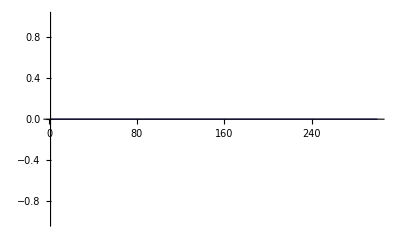

```mathematica
DiscretePlot[Re[tdifx[n,N@Im@ZetaZero@1]],{n,1,300}]
```

```mathematica
FullSimplify[(j/n)^(-1/2)Cos[s Log[j/n]]+I(j/n)^(-1/2)Sin[s Log[j/n]]]
```

(j/n)^(-1/2+ⅈ s)

```mathematica
Integrate[Tan[s Log[x]]/x^(1/2),{x,0,1}]
```

$Aborted

```mathematica
tlogsin[n_,s_]:=n(1/n Sum[(j/n)^(-1/2)(j/n)Sin[s Log[j/n]],{j,1,n}]-(-(4 s)/(9+4 s^2)))
```

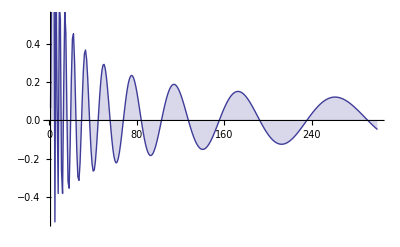

```mathematica
DiscretePlot[Re[tlogsin[n,N@Im@ZetaZero@1+1]],{n,1,300}]
```

```mathematica
FullSimplify[-(2/(1+4 s^2))+I(-(-(4 s)/(1+4 s^2)))]
```

(2 ⅈ)/(-ⅈ+2 s)

```mathematica
Integrate[x^(-1/2+s I),{x,0,1}]
```

ConditionalExpression[(2 ⅈ)/(ⅈ-2 s),Im[s]<1/2]

```mathematica
FullSimplify@Integrate[Sin[s Log[x]+c]/x^(1/2),{x,0,1}]
```

(2 (-2 s Cos[c]+Sin[c]))/(1+4 s^2)

```mathematica
(2 (-2 s Cos[c]+Sin[c]))/(1+4 s^2)/.c->Pi/4
```

(2 (1/(√2)-√2 s))/(1+4 s^2)

```mathematica
(2 (-2 s Cos[c]+Sin[c]))/(1+4 s^2)/.c->3Pi/4
```

(2 (1/(√2)+√2 s))/(1+4 s^2)

```mathematica
(2 (-2 s Cos[c]+Sin[c]))/(1+4 s^2)/.c->0
```

-(4 s)/(1+4 s^2)

```mathematica
(2 (-2 s Cos[c]+Sin[c]))/(1+4 s^2)/.c->Pi/2
```

2/(1+4 s^2)

```mathematica
cc[c_]:=(2 (-2 s Cos[c]+Sin[c]))/(1+4 s^2)
```

```mathematica
cc[0]/cc[Pi/2]
```

-2 s

```mathematica
cc[Pi/4]/cc[3Pi/4]
```

(1/(√2)-√2 s)/(1/(√2)+√2 s)

```mathematica
cc[3Pi/4]/cc[Pi/4]
```

(1/(√2)+√2 s)/(1/(√2)-√2 s)

```mathematica
(** 2s and 1 vs 1 and 1/(2s)}
```

```mathematica
(2s)^(1/2)
```

√2 √s

```mathematica
(2s)/(√2 √s)
```

√2 √s

```mathematica
1/(√2 √s)
```

1/(√2 √s)

```mathematica
FullSimplify[((1/(√2)+√2 s)/(1/(√2)-√2 s))^(1/2)]
```

√((1+2 s)/(1-2 s))

```mathematica
FullSimplify[((1/(√2)-√2 s)/(1/(√2)+√2 s))*(√((1+2 s)/(1-2 s)))]
```

1/(√((1+2 s)/(1-2 s)))

```mathematica
FullSimplify[((1/(√2)+√2 s)/(1/(√2)-√2 s))*(√((1+2 s)/(1-2 s)))]
```

-(√(1/(1-2 s)) (1+2 s)^(3/2))/(-1+2 s)

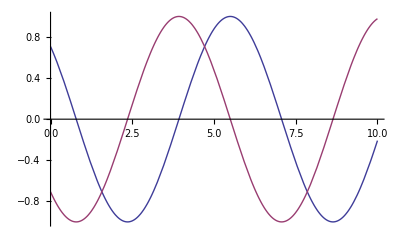

```mathematica
Plot[{Sin[x+3Pi/4],-Sin[x+Pi/4]},{x,0,10}]
```

```mathematica
ach[s_]:={(√2 √s),1/(√2 √s)}
ach2[s_]:=FullSimplify[{√(-1+2/(1+2 s)),1/√(-1+2/(1+2 s))}]
```

```mathematica
ach2[200]
```

{ⅈ √(399/401),-ⅈ √(401/399)}

```mathematica
FullSimplify[((1/(√2)-√2 s)/(1/(√2)+√2 s))^(1/2)]
```

√(-1+2/(1+2 s))

```mathematica
(-1(1/2+s)+1)/(1/2+ s)
```

(1/2-s)/(1/2+s)

```mathematica
((1/2-s)/(1/2+s))^(1/2)
```

√((1/2-s)/(1/2+s))

```mathematica
Integrate[Sin[s Log[x]+Pi/4]/x^(1/2),{x,0,1}]
```

ConditionalExpression[(√2 (1-2 s))/(1+4 s^2),-1/2<Im[s]<1/2]

```mathematica
Integrate[Sin[s Log[x]-Pi/4]/x^(1/2),{x,0,1}]
```

ConditionalExpression[-(√2 (1+2 s))/(1+4 s^2),-1/2<Im[s]<1/2]

```mathematica
tsinp[n_,s_]:=n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]+Pi/4],{j,1,n}]-((√2 (1-2 s))/(1+4 s^2)))
tsinm[n_,s_]:=n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]-Pi/4],{j,1,n}]-(-(√2 (1+2 s))/(1+4 s^2)))
tsinpm[n_,s_]:=tsinp[n,s]+tsinm[n,s]
tsinpm2[n_,s_]:=(n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]+Pi/4],{j,1,n}]-((√2 (1-2 s))/(1+4 s^2))))+(n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]-Pi/4],{j,1,n}]-(-(√2 (1+2 s))/(1+4 s^2))))
tsinpm3[n_,s_]:=(1/√(-(1/2-s)/(1/2+s)))(n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]+Pi/4],{j,1,n}]))-√(-(1/2-s)/(1/2+s))(n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]-Pi/4],{j,1,n}]))-2^(1/2)/2
tsinpm4[n_,s_]:=(n(1/n Sum[(j/n)^(-1/2)(1/√(-(1/2-s)/(1/2+s)))Sin[s Log[j/n]+Pi/4],{j,1,n}]))-(n(1/n Sum[(j/n)^(-1/2)(√(-(1/2-s)/(1/2+s)))Sin[s Log[j/n]-Pi/4],{j,1,n}]))-2^(1/2)/2
tsinpm5[n_,s_]:=n(1/n Sum[(j/n)^(-1/2)((1/√(-(1/2-s)/(1/2+s)))Sin[s Log[j/n]+Pi/4]-(√(-(1/2-s)/(1/2+s)))Sin[s Log[j/n]-Pi/4]),{j,1,n}])
```

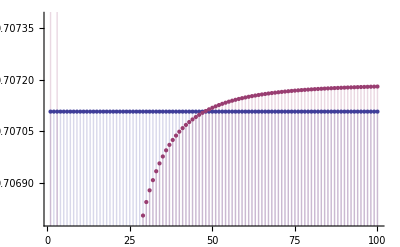

```mathematica
DiscretePlot[{2^(1/2)/2,Re@tsinpm5[n,N@Im@ZetaZero@5]},{n,1,100}]
```

```mathematica
(((√2 (1-2 s))/(1+4 s^2))/(-(√2 (1+2 s))/(1+4 s^2)))
```

-(1-2 s)/(1+2 s)

```mathematica
((-(√2 (1+2 s))/(1+4 s^2))/((√2 (1-2 s))/(1+4 s^2)))
```

-(1+2 s)/(1-2 s)

```mathematica
(-(1-2 s)/(1+2 s))^(1/2)
```

√(-(1-2 s)/(1+2 s))

```mathematica
2^.5/2
```

0.707107

```mathematica
N@2^(1/2)/2
```

0.707107

```mathematica
1/N@Im@ZetaZero@1
```

0.0707477

```mathematica
((.5^2)+(1/N@Im@ZetaZero@1)^2)^.5
```

0.50498

```mathematica
1*Sin[Pi/4.]+21/Im@ZetaZero@1*Sin[-Pi/4]
```

-0.343444

```mathematica
(** n(1/n Sum[(j/n)^(-1/2)((1/√(-(1/2-s)/(1/2+s)))Sin[s Log[j/n]+Pi/4]-(√(-(1/2-s)/(1/2+s)))Sin[s Log[j/n]-Pi/4]),{j,1,n}]) **)
tsinhalf[n_,s_]:=2n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]+Pi/4],{j,1,n}]-((√2 (1-2 s))/(1+4 s^2)))-1/(√2)
tsinmhalf[n_,s_]:=2n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]-Pi/4],{j,1,n}]-(-(√2 (1+2 s))/(1+4 s^2)))-(-1/(√2))
tsinthird[n_,s_]:=2n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]+Pi/6],{j,1,n}]-((1-2 √3 s)/(1+4 s^2)))-1/2
tmid[n_,s_]:=(2n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]+Pi/4],{j,1,n}]-((√2 (1-2 s))/(1+4 s^2)))-1/(√2))-(2n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]-Pi/4],{j,1,n}]-(-(√2 (1+2 s))/(1+4 s^2)))-(-1/(√2)))
tmid2[n_,s_]:=(2n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]+Pi/4],{j,1,n}]-((√2 (1-2 s))/(1+4 s^2)))-1/(√2))1/√(-(1/2-s)/(1/2+s))-(2n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]-Pi/4],{j,1,n}]-(-(√2 (1+2 s))/(1+4 s^2)))-(-1/(√2)))√(-(1/2-s)/(1/2+s))
tmid3[n_,s_]:=(2n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]+Pi/4],{j,1,n}])-1/(√2))1/√(-(1/2-s)/(1/2+s))-(2n(1/n Sum[(j/n)^(-1/2)Sin[s Log[j/n]-Pi/4],{j,1,n}])-(-1/(√2)))√(-(1/2-s)/(1/2+s))
tmid4[n_,s_]:=(n(1/n Sum[(j/n)^(-1/2)(1/√(-(1/2-s)/(1/2+s)))Sin[s Log[j/n]+Pi/4],{j,1,n}])-1/(2 √2)/√(-(1/2-s)/(1/2+s)))-(n(1/n Sum[(j/n)^(-1/2)√(-(1/2-s)/(1/2+s))Sin[s Log[j/n]-Pi/4],{j,1,n}])-(-1/(2 √2))√(-(1/2-s)/(1/2+s)))
tmid5[n_,s_]:=(n(1/n Sum[(j/n)^(-1/2)(1/√(-(1/2-s)/(1/2+s)))Sin[s Log[j/n]+Pi/4],{j,1,n}]))-(n(1/n Sum[(j/n)^(-1/2)√(-(1/2-s)/(1/2+s))Sin[s Log[j/n]-Pi/4],{j,1,n}]))-1/(2 √2)/√(-(1/2-s)/(1/2+s))+(-1/(2 √2))√(-(1/2-s)/(1/2+s))
tmid6[n_,s_]:=(( Sum[(j/n)^(-1/2)(1/√(-(1/2-s)/(1/2+s)))Sin[s Log[j/n]+Pi/4],{j,1,n}]))-(( Sum[(j/n)^(-1/2)√(-(1/2-s)/(1/2+s))Sin[s Log[j/n]-Pi/4],{j,1,n}]))-1/(2 √2)/√(-(1/2-s)/(1/2+s))+(-1/(2 √2))√(-(1/2-s)/(1/2+s))
tmid7[n_,s_]:=(( Sum[(j/n)^(-1/2)((1/√(-(1/2-s)/(1/2+s)))Sin[s Log[j/n]+Pi/4]-√(-(1/2-s)/(1/2+s))Sin[s Log[j/n]-Pi/4]),{j,1,n}]))-1/(2 √2)/√(-(1/2-s)/(1/2+s))+(-1/(2 √2))√(-(1/2-s)/(1/2+s))
tmid8[n_,s_]:=Sum[(j/n)^(-1/2)((√(-(1/2-s)/(1/2+s)))^-1 Sin[s Log[j/n]+Pi/4]-√(-(1/2-s)/(1/2+s))Sin[s Log[j/n]-Pi/4]),{j,1,n}]-s/(√(-1/2+s) √(1/2+ s)2^(1/2))
tmid9[n_,s_]:=Sum[(j/n)^(-1/2)((-(1/2-s)/(1/2+s))^(-1/2) Sin[s Log[j/n]+Pi/4]-(-(1/2-s)/(1/2+s))^(1/2)Sin[s Log[j/n]-Pi/4]),{j,1,n}]-s/(√(-1/2+s) √(1/2+ s)2^(1/2))
tmid10[n_,s_]:=Sum[(j/n)^(-1/2)((-(1/2-s)/(1/2+s))^(-1/2)(1/(2I))( E^(I(s Log[j/n]+Pi/4))-E^(-I(s Log[j/n]+Pi/4)))-(-(1/2-s)/(1/2+s))^(1/2)(1/(2I))(E^(I(s Log[j/n]-Pi/4))-E^(-I(s Log[j/n]-Pi/4)))),{j,1,n}]-s/(√(-1/2+s) √(1/2+ s)2^(1/2))
tmid11[n_,s_]:=(1/(2I))Sum[(j/n)^(-1/2)((-(1/2-s)/(1/2+s))^(-1/2)( E^(I(s Log[j/n]+Pi/4))-E^(-I(s Log[j/n]+Pi/4)))-(-(1/2-s)/(1/2+s))^(1/2)(E^(I(s Log[j/n]-Pi/4))-E^(-I(s Log[j/n]-Pi/4)))),{j,1,n}]-s/(√(-1/2+s) √(1/2+ s)2^(1/2))
tmid12[n_,s_]:=(1/(2I))Sum[(j/n)^(-1/2)(E^((-1/2)Log[(-(1/2-s)/(1/2+s))])( E^(I(s Log[j/n]+Pi/4))-E^(-I(s Log[j/n]+Pi/4)))-E^(1/2Log[(-(1/2-s)/(1/2+s))])(E^(I(s Log[j/n]-Pi/4))-E^(-I(s Log[j/n]-Pi/4)))),{j,1,n}]-s/(√(-1/2+s) √(1/2+ s)2^(1/2))
tmid13[n_,s_]:=(1/(2I))Sum[(j/n)^(-1/2)(E^((-1/2)Log[(-(1/2-s)/(1/2+s))])( E^(I(s Log[j/n]+Pi/4))-E^(-I(s Log[j/n]+Pi/4)))-E^(1/2Log[(-(1/2-s)/(1/2+s))])(E^(I(s Log[j/n]-Pi/4))-E^(-I(s Log[j/n]-Pi/4)))),{j,1,n}]-s/(√(-1/2+s) √(1/2+ s)2^(1/2))
tmid14[n_,s_]:=(1/(2I))Sum[(j/n)^(-1/2)(( E^(I(s Log[j/n]+Pi/4)+(-1/2)Log[(-(1/2-s)/(1/2+s))])-E^(-I(s Log[j/n]+Pi/4)+(-1/2)Log[(-(1/2-s)/(1/2+s))]))-(E^(-1/2Log[(-(1/2-s)/(1/2+s))]+I(s Log[j/n]-Pi/4))-E^(-1/2Log[(-(1/2-s)/(1/2+s))]-I(s Log[j/n]-Pi/4)))),{j,1,n}]-s/(√(-1/2+s) √(1/2+ s)2^(1/2))
```

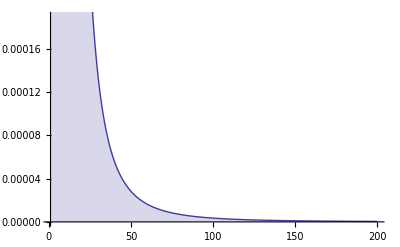

```mathematica
DiscretePlot[Abs@tmid13[n,N@Im@ZetaZero@2],{n,1,200}]
```

```mathematica
FullSimplify[-1/(2 √2)/√(-(1/2-s)/(1/2+s))+(-1/(2 √2))√(-(1/2-s)/(1/2+s))]
```

-s/(√(-1/2+s) √(1+2 s))

```mathematica
N[(1/√(-(1/2-s)/(1/2+s)))Sin[s Log[j/n]+Pi/4]-√(-(1/2-s)/(1/2+s))Sin[s Log[j/n]-Pi/4]/.s->1000000]
```

1. Sin[0.785398-1.×10^6 Log[j/n]]+1. Sin[0.785398+1.×10^6 Log[j/n]]

```mathematica
(√(-(1/2-s)/(1/2+s)))^-1
```

1/(√(1-2/(1+2 s)))

-1/2 Log[-1+2 s]+1/2 Log[1+2 s]

```mathematica
TrigToExp[Sin[x]]
```

1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)

```mathematica
Log[(-(1/2-s)/(1/2+s))]/.s->4.3
```

-0.233615

```mathematica
Log[((1/2-s)/(1/2+s))]/.s->4.3
```

-0.233615+3.14159 ⅈ

```mathematica
Log[((1/2-s)/(1/2+s))]-Pi I/.s->4.3
```

-0.233615+0. ⅈ

```mathematica
Log[1/2-s]-Log[1/2+s]-Pi I/.s->(1/4)t
```

-ⅈ π+Log[1/2-t/4]-Log[1/2+t/4]

```mathematica
TrigToExp[ArcTanh[s]]
```

-1/2 Log[1-s]+1/2 Log[1+s]

```mathematica
ss[n_,s_]:=Sum[j^(-1/2)Sin[s Log[n/j]-ArcTan[2s]]/Sin[s Log[n]-ArcTan[2s]],{j,1,n}]
ssa[n_,s_]:=Sum[j^(-1/2)Sin[s Log[n]-s Log[j]-ArcTan[2s]]/Sin[s Log[n]-ArcTan[2s]],{j,1,n}]
ssb[n_,s_]:=Sum[j^(-1/2)Cos[s Log[n]-s Log[j]+ArcCot[2s]]/Cos[s Log[n]+ArcCot[2s]],{j,1,n}]
ssbd[n_,j_,s_]:=j^(-1/2)Cos[s Log[n]-s Log[j]+ArcCot[2s]]/Cos[s Log[n]+ArcCot[2s]]
tt[n_,s_]:=Sum[j^(-1/2)(Cos[s Log[j]]+Tan[s Log[n]+ArcCot[2s]]Sin[s Log[j]]),{j,1,n}]
```

```mathematica
Chop@ssb[10000,1.5I]
```

1.64493

```mathematica
Zeta[2.]
```

1.64493

```mathematica
Integrate[Sin[s Log[x]+ArcTan[2s]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[0,-1/2<Im[s]<1/2]

```mathematica
N@ArcTan[2 4I ]
```

1.5708+0.125657 ⅈ

```mathematica
N@Pi/2
```

1.5708

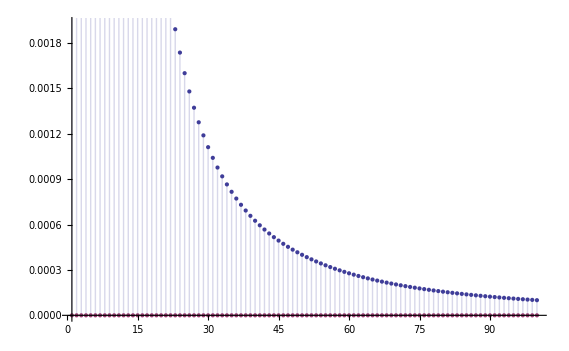

```mathematica
DiscretePlot[{Re[ssbd[4000,n,1.5 I]],0},{n,1,100}]
```

```mathematica
e1[x_,t_]:=2t Cos[t Log[x]]+Sin[t Log[x]]
e2[x_,t_]:= (Sin[t Log[x]+ArcTan[2t]]) (2t)^(1/2)
```

```mathematica
N@e1[100,2]
```

-3.69559

```mathematica
N@e2[100,2]
```

-1.79262

```mathematica
qq[n_,s_]:= Sum[j^(-1/2)Sin[s Log[n/j]-ArcTan[2s]],{j,1,n}]
qqa[n_,s_]:=Sum[j^(-1/2)Sin[s Log[n/j]],{j,1,n}]
qq2[n_,s_]:=n^(1/2) ((1/n)Sum[(n/j)^(1/2)Sin[s Log[n/j]-ArcTan[2s]],{j,1,n}])
```

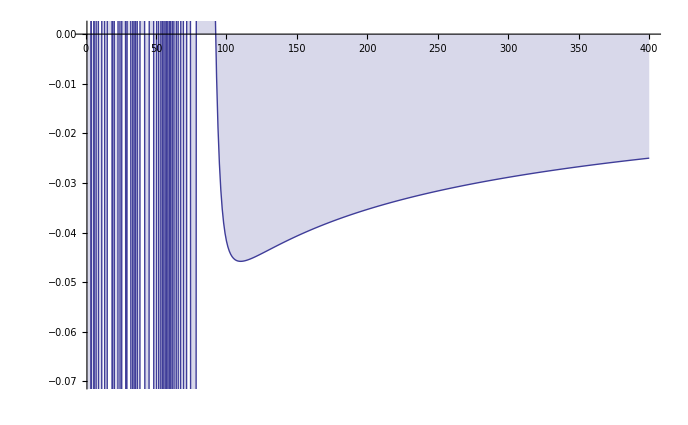

```mathematica
DiscretePlot[Re@qq[n,Im@N@ZetaZero@300],{n,1,400}]
```

```mathematica
(Integrate[x^(-1/2)Sin[-s Log[x]-ArcTan[2s]],{x,0,1}])
```

ConditionalExpression[0,-1/2<Im[s]<1/2]

```mathematica
Im@N@ZetaZero@300
```

541.847

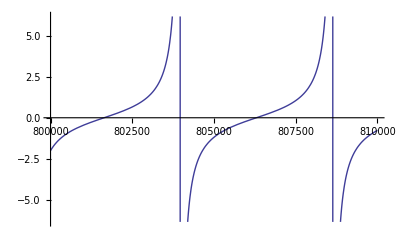

```mathematica
Plot[Im@Tanh[s Log[n]-ArcTanh[1/(2s)]]/.s->Im@N@ZetaZero@300 I+.3I,{n,800000,810000}]
```

```mathematica
-8s/(1+4s^2)/(2s)^(1/2)
```

-(4 √2 √s)/(1+4 s^2)

```mathematica
-4/(1+4s^2) (2s)^(1/2)
```

-(4 √2 √s)/(1+4 s^2)